```mathematica
Clear["Global`*"];
f = 1/4/π/Df/τ*Exp[-(x^2+y^2)/4/Df/τ]
```

(ⅇ^((-x^2-y^2)/(4 Df τ)))/(4 Df π τ)

```mathematica
Assuming[Df>0&&T>0, 1/T*Integrate[f,{x,-∞,∞},{y,-∞,∞},{τ,0,T}]]
```

1

```mathematica
J = Assuming[Df≥0&&T≥0, 1/T*Integrate[r^3/2/Df/τ*Exp[-r^2/4/Df/τ],{r,0,∞},{τ,0,T}]]
```

2 Df T

```mathematica
J = Assuming[Df>0&&T>0, 1/T*Integrate[(x^2+y^2)*f,{x,-∞,∞},{y,-∞,∞},{τ,0,T}]]
```

2 Df T

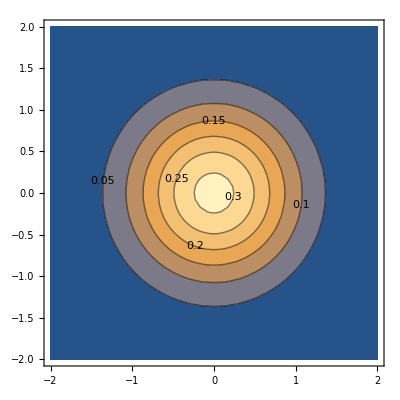

```mathematica
ContourPlot[f/.{τ->10,Df-> 0.025},{x,-2,2},{y,-2,2},ContourLabels->True]
```

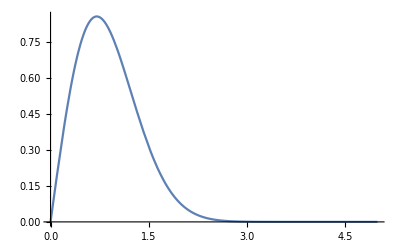

```mathematica
l=0.1;
dt = 0.1;
Df=l^2/4/dt;
τ=10.0;
fr = r/2/Df/τ*Exp[-r^2/4/Df/τ];
Plot[fr,{r,0,5}]
```

```mathematica
FindMaximum[fr,r]
```

{0.857764,{r→0.707107}}